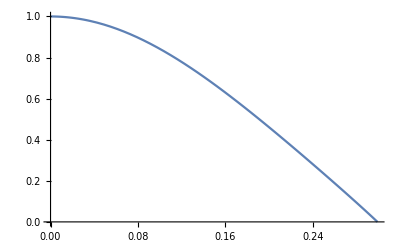

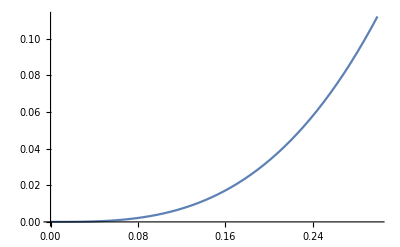

Radius=0.299206

Mass=0.112202

```mathematica
ρ0:=1
(*m[r]:=4/3 π r^3 ρ0*)
my0=1*10^(-9);
pc:=1
eqnM:={m'[r]==4 π r^2 ρ0}
condM:={m[my0]==0}
eqnP:={-p'[r]==(ρ0+p[r])*(m[r]+4*π*r^3*p[r])/(r^2*(1-2*m[r]/r))}
condP:={p[my0]==pc}
stopCond:={WhenEvent[p[r]==0,rMax=r;"StopIntegration"]}
system:=Join[eqnM,eqnP,condM,condP,stopCond];
state=First[NDSolve`ProcessEquations[system, {p,m}, {r, my0, ∞}]];
NDSolve`Iterate[state,∞]
sol=NDSolve`ProcessSolutions[state];
(*sol=NDSolve[system, {p}, {r, my0, ∞}];*)
Plot[Evaluate[p[r]/.First[sol]],{r,my0,rMax}]
Plot[Evaluate[m[r]/.sol],{r,my0,rMax}]
Print["Radius=",rMax,""];
Print["Mass=",Evaluate[m[rMax]/.sol],""];
```